1D (“pancake”) Schrödinger-Poisson solver on Einstein-de Sitter background
used in arXiv:1403.5567  michael.kopp@physik.lmu.de

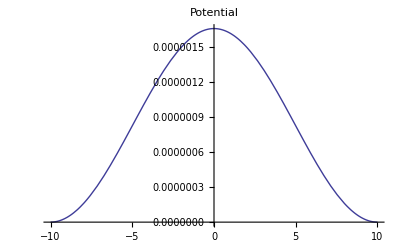
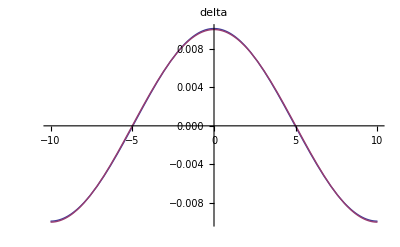
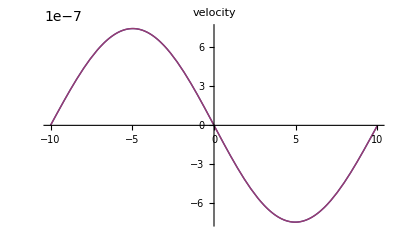

```mathematica
(*precision: this is only to avoid Mathematica complaining about stuff having less than Workingprecision*)
prec=40; 
(*initial width of overdensity in Mpc*)
bs=10;
(*initial scale factor*)
ai=SetPrecision[0.01,prec];
(*hbar/mass= 10^(-5) * bs, is already quite big. Better choose smaller *)
hbar=SetPrecision[0.0001 ,prec]; 
(*Hubble parameter*)
Hub[a_]:=H0 √(om/a^3+(1-om));
(*DM density*)
rhom[a_]:=3/(8 Pi GN)H0^2 om 1/a^3
(*H0 = h 100 km/(s Mpc)*)
h=SetPrecision[0.70 ,prec];
(*Subscript[Ω, m]=Subscript[Ω, cdm]+Subscript[Ω, b]*)
om=SetPrecision[1,prec]; 
 (*primordial spectral index*)
ns=SetPrecision[0.95,prec]; 
  (*turns grams into Msol*)
gramstoMsol=SetPrecision[1/(1.99 10^(33)),prec]; 
(*turns cm into Mpc*)
cmtoMpc=SetPrecision[1/(3.086 10^(24)),prec]; 
 (*turns cm/s into 1*)
cmpersectoOne=SetPrecision[ 1/(2.998 10^(10)),prec]; 
(*Newton constant in units Mpc/Msol and c=1*)
GN=SetPrecision[ 6.672 10^(-8) cmtoMpc cmpersectoOne^2/(gramstoMsol),prec];  
(*Hubble today in inverse Mpc*)
H0=h(100 10^5 cmpersectoOne); 
Dgra[a_]:=a
dDgrada[a_]:=1
(*initial nonlinear density, Zeldovich: 1/(1+d displ/dx),d displ/dx = - deltalin *)

displ[q_,a_]:=-Dgra[a]Sin[ Pi q/bs]/(Pi/bs)
qofx[x_?NumericQ,a_?NumericQ]:=q2/.FindRoot[x== q2+displ[q2,a],{q2,x}]
(*initial linear density fluctuation, linearly extrapolated*)
deltalin[q_,a_]:=Dgra[a] Cos[ Pi q/bs]
(*v = a dx/dt = a dota dx/da*)
(* Zeldovich stuff*)
velZelq[q_,a_]:=-a^2 Hub[a]dDgrada[a] Sin[ Pi q/bs]/(Pi/bs)
deltaZelq[q_,a_]:=1/(1-deltalin[q,a])-1
qtab[a_?NumericQ]:=qtab[a]=Table[{x1,qofx[x1,a]},{x1,-bs,bs,0.1}];
qtabINT[a_?NumericQ]:=qtabINT[a]=Interpolation[qtab[a]]
deltaZel[x_,a_]=deltaZelq[qtabINT[a][x],a];
velZel[x_,a_]:=velZelq[qtabINT[a][x],a]
(*Newtonian potential of linearly extrapolated delta*)
potexactlin[x_]:=-ai^2 4 Pi GN/(Pi/bs)^2 rhom[ai](deltalin[x,ai]+deltalin[0,ai])
(*Initial Zeldovich stuff*)
qinitab=Table[{x,qofx[x,ai]},{x,-bs,bs,0.1}];
qinitabINT=Interpolation[qinitab];
deltaZelini[x_]:=deltaZelq[qinitabINT[x],ai]
velZelini[x_]:=velZelq[qinitabINT[x],ai]


(*Plots the arg of a complex function*)
SetAttributes[argPlot,HoldAll];
Options[argPlot]=Options[Plot];
argPlot[exp_,{x_,x0_,x1_},opt:OptionsPattern[argPlot]]:=Module[{pts,pl},pl=Plot[Arg[exp],{x,x0,x1},PlotRange->All,PlotPoints->OptionValue[PlotPoints]];
pts=SortBy[Cases[pl,Line[pts_]:>pts,Infinity],#[[1,1]]&];
pts=Reap[Fold[Module[{ptsn},ptsn=#2;
ptsn[[All,2]]-=Round[ptsn[[1,2]]-#1,2 Pi];
Sow[ptsn];
ptsn[[-1,2]]]&,0,pts];][[2,1]];
ListLinePlot[Flatten[pts,1],opt]]

(*Initial Newtonian potential*)
solini=NDSolve[{g''[x]== ai^2 4 Pi GN rhom[ai] deltaZelini[x],g[-bs]==g[bs]==0},g,{x,-bs,bs},MaxStepSize->0.1,PrecisionGoal->15,AccuracyGoal->15,Method->"StiffnessSwitching"][[1]];

(*spatialgrid*)
gridlength=1401;
spacegridh=Partition[Range[-bs,bs,2.bs/(gridlength-1)],1];




(*Initial times for PDE solver and snapshot saver*)
timenow=ai;
timenow2=ai;
(*maximal scale factor*)
maxtime=2;
(*timestep decides the time during which the Newtonian potential is kept constant*)
timestep=0.001;
(*timestep2 decides how many snapshots are dumped*)
timestep2=0.05;
dmax=1000;


(*Initial conditions*)
delta[x_]=deltaZelini[x];
solpot[x_]=Evaluate[g[x]/.solini];
phipot[x_]=-2/(3 Hub[ai])solpot[x];
Psisol[x_]=Sqrt[delta[x]+1]Exp[I phipot[x]/hbar];
dsolpotda[x_]=0;
timelist={ai};
usol[x_]=ai velZelini[x];
{Plot[{-g[x]/.solini},{x,-bs,bs},PlotRange->All,PlotLabel->"Potential"],Plot[{delta[x],deltalin[x,ai]},{x,-bs,bs},PlotRange->All,PlotLabel->"delta"],Plot[{phipot'[x],usol[x]},{x,-bs,bs},PlotRange->All,PlotLabel->"velocity"]}
timelist={ai};
goal=13+Floor[Log[ai]];
spacetimegridh=Partition[Join[spacegridh,Evaluate[Table[{ai},{i,1,Length[spacegridh]}]],2],1];potdata=Join[spacetimegridh,Derivative[0][solpot][spacegridh],2];
(*initialize lists to dump field*)
psicollecth={};
potcollecth={};
potdata=Join[spacetimegridh,Derivative[0][solpot][spacegridh],2];
potcollecth=AppendTo[potcollecth,potdata];psidata=Join[spacetimegridh,Derivative[0][Psisol][spacegridh],2];psicollecth=AppendTo[psicollecth,psidata];
(*Note that from the delta plot that Zeldovich stuff is not necessary and linear is enough *)
```

```mathematica
Monitor[While[timenow<maxtime,
(*this increases the Precisiongoal and AccuracyGoal over time*)
goal=14+Floor[Log[timenow]/2];
(*this solves the Schrödinger equation between two Poisson updates: timenow,timelast+timestep*)solh=NDSolve[{a^3 Hub[a]I hbar Derivative[0,1][Psi][x,a]==-hbar^2/2  Derivative[2,0][Psi][x,a]+Psi[x,a] a^2 solpot[x],Psi[x,timenow]== Psisol[x],Psi[-bs,a]==Psi[bs,a] },{Psi},{x,-bs,bs},{a,timenow,timenow+timestep},PrecisionGoal->goal,AccuracyGoal->Floor[goal/2],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->gridlength,"MaxPoints"->gridlength(*,If[timenow>1,"DifferenceOrder"->"Pseudospectral","DifferenceOrder"->Automatic](*switch "Pseudospectral" on to get a more stable solution, very slow!!!*)*)},Method->"StiffnessSwitching"},StepMonitor:>(delta[x_]=Re[(Psi[x,a]Conjugate[Psi[x,a]]-1)] ;Psisol[x_]=Psi[x,a];time=a;)];

(*this solves the Poisson equation*)solf=NDSolve[{g''[x]== 4 Pi GN time^2 rhom[time]  delta[x],g[-bs]==g[bs]==0},g,{x,-bs,bs},PrecisionGoal->15,AccuracyGoal->15,Method->"StiffnessSwitching"][[1]]; solpot[x_]=Evaluate[g[x]/.solf];

(*this dumps the fields every timestep2*)
If[time≥timenow2+timestep2-ai,{spacetimegridh=Partition[Join[spacegridh,Evaluate[Table[{time},{i,1,Length[spacegridh]}]],2],1];potdata=Join[spacetimegridh,Derivative[0][solpot][spacegridh],2];potcollecth=AppendTo[potcollecth,potdata];psidata=Join[spacetimegridh,Derivative[0][Psisol][spacegridh],2];psicollecth=AppendTo[psicollecth,psidata];
(*Export["~/SchroedingerPsi.m",psicollecth];*)
timenow2=time}];
timenow=time;

] , 


(*this monitors the solution*){Plot[{delta[x],deltalin[x,time]},{x,-bs,bs},PlotRange->All,PlotLabel->{"δ=",delta[0],"a=",time}],Plot[{-solpot[x]},{x,-bs,bs},PlotRange->All,PlotLabel->{"V=",solpot[0],"a=",time}],argPlot[{Psisol[x]},{x,-bs,bs},PlotRange->All,PlotLabel->{"ϕ=",phipot[0],"a=",time}]}]
```

```mathematica
(*plot it*)
PsiInt=Interpolation[Flatten[psicollecth,1]];
Manipulate[{Plot[Abs[PsiInt[x,a]],{x,-10,10}],Plot[Arg[PsiInt[x,a]],{x,-10,10}]},{a,ai+timestep2,timenow2}]
```

```mathematica
(*this writes the solution into a file*)
Export["~/SchroedingerPsi.m",psicollecth];
Export["~/SchroedingerPot.m",potcollecth];
```